## Definitions and EOM in GG gauge

```mathematica
ain[t_,r_]=A0[t,r]+A1[t,r](D-3)+A2[t,r](D-3)^2;
U[t_,r_]=u0[t,r]+u1[t,r](D-3)+u2[t,r](D-3)^2;
V[t_,r_]=v0[t,r]+v1[t,r](D-3)+v2[t,r](D-3)^2;
f[t_,r_]=1+f1[t,r](D-3)+f2[t,r](D-3)^2;
```

```mathematica
eom1=D[ain[t,r],r]-(8(D-3)-(8(D-3)+(D-2)^3(U[t,r]^2+V[t,r]^2))ain[t,r])/(8r)//Simplify;
eom2=D[f[t,r],r]-(D-3)(1/ain[t,r]-1)f[t,r]/r//Simplify;
eom3=D[U[t,r],r]-(f[t,r]((D-2-2(D-3)/ain[t,r])U[t,r]+(D-2)V[t,r])-2r D[U[t,r],t])/(2r(f[t,r]+r))//Simplify;
eom4=D[V[t,r],r]-(f[t,r]((D-2-2(D-3)/ain[t,r])V[t,r]+(D-2)U[t,r])+2r D[V[t,r],t])/(2r(f[t,r]-r))//Simplify;
eom5=D[ain[t,r],t]+D-3-((D-2)^3((f[t,r]+r)U[t,r]^2-(f[t,r]-r)V[t,r]^2)/(8r)+D-3)ain[t,r]//Simplify;
```

## Small D expansion to LO and NLO

```mathematica
ser1=Series[eom1,{D,3,1}]//Simplify;
```

```mathematica
ser2=Series[eom2,{D,3,2}]//Simplify;
```

```mathematica
ser3=Series[eom3 ,{D,3,1}]//Simplify;
```

```mathematica
ser4=Series[eom4 ,{D,3,1}]//Simplify;
```

```mathematica
ser5=Series[eom5,{D,3,1}]//Simplify;
```

## Five LO PDEs

```mathematica
replu0v0=Solve[{PILO[t,r]==(u0[t,r]+v0[t,r])/(2r),PSILO[t,r]==(v0[t,r]-u0[t,r])/(2r^2)},{u0[t,r],v0[t,r]}][[1]]
```

{u0[t,r]→r PILO[t,r]-r^2 PSILO[t,r],v0[t,r]→r PILO[t,r]+r^2 PSILO[t,r]}

```mathematica
LOeq1=Normal[ser1]/.D->3//Simplify
```

(A0[t,r] (u0[t,r]^2+v0[t,r]^2))/(8 r)+A0^(0,1)[t,r]

```mathematica
LOeq2=Normal[ser5]/.D->3//Simplify
```

-(A0[t,r] ((1+r) u0[t,r]^2+(-1+r) v0[t,r]^2))/(8 r)+A0^(1,0)[t,r]

```mathematica
LOeq3=Normal[ser2/(D-3)]/.D->3
```

(1-1/A0[t,r])/r+f1^(0,1)[t,r]

```mathematica
LOeq4=Normal[ser3]/.D->3//Simplify
```

u0^(0,1)[t,r]-(u0[t,r]+v0[t,r]-2 r u0^(1,0)[t,r])/(2 r+2 r^2)

```mathematica
(* the last eq. is tricky due to the potential singularity at r=1 which competes with the small eps term near the SSH *)
LOeq5=(eom4//Simplify)/.(1-r+(-3+D) f1[t,r]+(-3+D)^2 f2[t,r])->denominator/.D->3/.denominator->(1-r+eps f1[t,r])
```

v0^(0,1)[t,r]-(u0[t,r]+v0[t,r]+2 r v0^(1,0)[t,r])/(2 r (1-r+eps f1[t,r]))

## Successful attempt to solve last 2 PDEs for eps=0

## Solve these two linear PDEs in this chapter

```mathematica
Normal[ser3]/.D->3
```

u0^(0,1)[t,r]-(u0[t,r]+v0[t,r]-2 r u0^(1,0)[t,r])/(2 r+2 r^2)

```mathematica
Normal[ser4]/.D->3
```

v0^(0,1)[t,r]+(u0[t,r]+v0[t,r]+2 r v0^(1,0)[t,r])/(2 (-1+r) r)

## Express in terms of Pi and Psi

```mathematica
replu0v0
```

{u0[t,r]→r PILO[t,r]-r^2 PSILO[t,r],v0[t,r]→r PILO[t,r]+r^2 PSILO[t,r]}

```mathematica
lineq1=(Normal[ser3]/.D->3/.replu0v0/.Derivative[0,1][u0][t,r]->D[u0[t,r]/.replu0v0,r]/.Derivative[1,0][u0][t,r]->D[u0[t,r]/.replu0v0,t])//Simplify
```

1/(1+r)r (PILO[t,r]-2 (1+r) PSILO[t,r]+PILO^(0,1)[t,r]+r PILO^(0,1)[t,r]-r PSILO^(0,1)[t,r]-r^2 PSILO^(0,1)[t,r]+PILO^(1,0)[t,r]-r PSILO^(1,0)[t,r])

```mathematica
lineq2=(Normal[ser4]/.D->3/.replu0v0/.Derivative[0,1][v0][t,r]->D[v0[t,r]/.replu0v0,r]/.Derivative[1,0][v0][t,r]->D[v0[t,r]/.replu0v0,t])//Simplify
```

r (PILO[t,r]/(-1+r)+2 PSILO[t,r]+PILO^(0,1)[t,r]+r PSILO^(0,1)[t,r]+(PILO^(1,0)[t,r])/(-1+r)+(r PSILO^(1,0)[t,r])/(-1+r))

## Use Fourier modes in time

```mathematica
lineq1A=Collect[Assuming[{k>-Infinity,t>-Infinity},((r lineq1//Simplify)/.PSILO[t,r]->Exp[I k t]psilo[r]/.Derivative[0,1][PSILO][t,r]->Exp[I k t]D[psilo[r],r]/.Derivative[1,0][PSILO][t,r]->I k Exp[I k t]psilo[r]/.PILO[t,r]->Exp[I k t]pilo[r]/.Derivative[0,1][PILO][t,r]->Exp[I k t]D[pilo[r],r]/.Derivative[1,0][PILO][t,r]->I k Exp[I k t]pilo[r])Exp[-I k t]/r^2//Simplify], pilo'[r]]
```

pilo'[r]+((1+ⅈ k) pilo[r]+(-2-2 r-ⅈ k r) psilo[r]-r (1+r) psilo'[r])/(1+r)

```mathematica
lineq2A=Collect[Assuming[{k>-Infinity,t>-Infinity},((lineq2//Simplify)/.PILO[t,r]->Exp[I k t]pilo[r]/.Derivative[0,1][PILO][t,r]->Exp[I k t]D[pilo[r],r]/.Derivative[1,0][PILO][t,r]->I k Exp[I k t]pilo[r]/.PSILO[t,r]->Exp[I k t]psilo[r]/.Derivative[0,1][PSILO][t,r]->Exp[I k t]D[psilo[r],r]/.Derivative[1,0][PSILO][t,r]->I k Exp[I k t]psilo[r])Exp[-I k t]/r//Simplify], pilo'[r]]
```

pilo'[r]+((1+ⅈ k) pilo[r]+(-2+2 r+ⅈ k r) psilo[r]+(-1+r) r psilo'[r])/(-1+r)

```mathematica
linpsieq=Collect[(lineq2A-lineq1A)/(2r)//Simplify, psilo'[r]]
```

((1+ⅈ k) pilo[r]+(-2+(2+ⅈ k) r^2) psilo[r])/(r (-1+r^2))+psilo'[r]

```mathematica
linpieq=Collect[(lineq2A+lineq1A)/(2)//Simplify, pilo'[r]]
```

((r+ⅈ k r) pilo[r]+ⅈ k r psilo[r])/(-1+r^2)+pilo'[r]

## Solve two first order ODEs in terms of 2F1 and MeijerG

```mathematica
solexactpipsi=Assuming[{r>0,r<1},DSolve[{linpieq==0,linpsieq==0},{pilo[r],psilo[r]},r]//Simplify][[1]]
```

{pilo[r]→C[1] Hypergeometric2F1[1/2+(ⅈ k)/2,1+(ⅈ k)/2,1,r^2]+C[2] MeijerG[{{},{-(ⅈ k)/2,-1/2 ⅈ (ⅈ+k)}},{{0,0},{}},r^2],psilo[r]→1/(2 k)(2 ⅈ C[1] Hypergeometric2F1[1/2+(ⅈ k)/2,1+(ⅈ k)/2,1,r^2]-2 k C[1] Hypergeometric2F1[1/2+(ⅈ k)/2,1+(ⅈ k)/2,1,r^2]-2 ⅈ C[1] Hypergeometric2F1[3/2+(ⅈ k)/2,2+(ⅈ k)/2,2,r^2]+3 k C[1] Hypergeometric2F1[3/2+(ⅈ k)/2,2+(ⅈ k)/2,2,r^2]+ⅈ k^2 C[1] Hypergeometric2F1[3/2+(ⅈ k)/2,2+(ⅈ k)/2,2,r^2]+2 ⅈ r^2 C[1] Hypergeometric2F1[3/2+(ⅈ k)/2,2+(ⅈ k)/2,2,r^2]-3 k r^2 C[1] Hypergeometric2F1[3/2+(ⅈ k)/2,2+(ⅈ k)/2,2,r^2]-ⅈ k^2 r^2 C[1] Hypergeometric2F1[3/2+(ⅈ k)/2,2+(ⅈ k)/2,2,r^2]+4 ⅈ C[2] MeijerG[{{},{-1-(ⅈ k)/2,-1/2 ⅈ (-ⅈ+k)}},{{-1,0},{}},r^2]-2 (-ⅈ+k) C[2] MeijerG[{{},{-(ⅈ k)/2,-1/2 ⅈ (ⅈ+k)}},{{0,0},{}},r^2]-4 ⅈ C[2] MeijerG[{{},{-(ⅈ k)/2,-1/2 ⅈ (ⅈ+k)}},{{0,1},{}},r^2])}

## Expanding near origin r=0 shows that regularity kills integration constant c2

```mathematica
D[Assuming[r>0,Series[pilo[r]/.solexactpipsi,{r,0,1}]],r]//FullSimplify
```

-(2^(-ⅈ k) C[2])/(√π Gamma[-ⅈ k] r)+O[r]^1

```mathematica
D[Assuming[r>0,Series[psilo[r]/.solexactpipsi,{r,0,0}]],r]//FullSimplify
```

-(2^(1-ⅈ k) C[2])/(√π Gamma[1-ⅈ k] r^3)+(2^(-1-ⅈ k) C[2])/(√π Gamma[-1-ⅈ k] r)+O[r]^0

```mathematica
replc=C[2]->0;
```

## Display solutions for Pi and Psi regular at r=0

```mathematica
pisol[r_]=Exp[I k t]pilo[r]/.solexactpipsi/.replc
```

ⅇ^(ⅈ k t) C[1] Hypergeometric2F1[1/2+(ⅈ k)/2,1+(ⅈ k)/2,1,r^2]

```mathematica
psisol[r_]=Exp[I k t]psilo[r]/.solexactpipsi/.replc//FullSimplify
```

-(ⅇ^(ⅈ k t) (-ⅈ+k) C[1] (Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]+(-1+r^2) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),1,r^2]))/(k r^2)

```mathematica
u0sol[t_,r_]=u0[t,r]/.replu0v0/.PILO[t,r]->pisol[r]/.PSILO[t,r]->psisol[r]//FullSimplify
```

1/k ⅇ^(ⅈ k t) C[1] ((-ⅈ+k+k r) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]+(-ⅈ+k) (-1+r^2) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),1,r^2])

```mathematica
v0sol[t_,r_]=v0[t,r]/.replu0v0/.PILO[t,r]->pisol[r]/.PSILO[t,r]->psisol[r]//FullSimplify
```

1/k ⅇ^(ⅈ k t) C[1] ((ⅈ+k (-1+r)) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]-(-ⅈ+k) (-1+r^2) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),1,r^2])

```mathematica
modeu0v0={u0[t,r]->u0sol[r],v0[t,r]->v0sol[r]};
```

```mathematica
(* this is psi for one Fourier mode *)
psi0sol[t_,r_]=(v0sol[t,r]-u0sol[t,r]-((v0sol[t,r]-u0sol[t,r])/.k->-k))/(2r^2)/.C[1]->cu[1]/2/I//Simplify
```

1/(2 k r^2)ⅇ^(-ⅈ k t) cu[1] ((1-ⅈ k) Hypergeometric2F1[1/2-(ⅈ k)/2,1-(ⅈ k)/2,1,r^2]+(1-ⅈ k) (-1+r^2) Hypergeometric2F1[1-(ⅈ k)/2,3/2-(ⅈ k)/2,1,r^2]+ⅇ^(2 ⅈ k t) (1+ⅈ k) (Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]+(-1+r^2) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),1,r^2]))

```mathematica
(* one Fourier mode of psi near the origin *)
Series[psi0sol[t,r],{r,0,3}]//FullSimplify
```

1/2 cu[1] (k Cos[k t]+Sin[k t])+1/16 cu[1] (-k (-11+k^2) Cos[k t]-6 (-1+k^2) Sin[k t]) r^2+O[r]^4

```mathematica
Nt=8;
```

```mathematica
four[t_,r_]=c[0]+Sum[c[k] ⅇ^(-2π*I*k/Δ t)+c[Nt-k] ⅇ^(2π*I*k/Δ t),{k,1,Nt/2-1}]+c[Nt/2]Cos[(π*Nt)/Δ t]//Simplify
```

c[0]+ⅇ^(-(2 ⅈ π t)/Δ) c[1]+ⅇ^(-(4 ⅈ π t)/Δ) c[2]+ⅇ^(-(6 ⅈ π t)/Δ) c[3]+ⅇ^((6 ⅈ π t)/Δ) c[5]+ⅇ^((4 ⅈ π t)/Δ) c[6]+ⅇ^((2 ⅈ π t)/Δ) c[7]+c[4] Cos[(8 π t)/Δ]

### Take odd modes for u0 at the origin and make them real

```mathematica
u0modeorigin[t_,r_]=Normal[Series[(u0sol[t,r])-(u0sol[t,r]/.k->-k)//FullSimplify,{r,0,10}]/.C[1]->cu[1]/2/I//FullSimplify]
```

r cu[1] Sin[k t]-1/2 r^2 cu[1] (k Cos[k t]+Sin[k t])+1/4 r^3 cu[1] (3 k Cos[k t]-(-2+k^2) Sin[k t])+1/16 r^4 cu[1] (k (-11+k^2) Cos[k t]+6 (-1+k^2) Sin[k t])+1/64 r^5 cu[1] (-10 k (-5+k^2) Cos[k t]+(24-35 k^2+k^4) Sin[k t])+1/384 r^6 cu[1] (-k (274-85 k^2+k^4) Cos[k t]-15 (8-15 k^2+k^4) Sin[k t])+(r^7 cu[1] (21 k (84-35 k^2+k^4) Cos[k t]-(-720+1624 k^2-175 k^4+k^6) Sin[k t]))/2304+(r^8 cu[1] (k (-13068+6769 k^2-322 k^4+k^6) Cos[k t]+28 (-180+469 k^2-70 k^4+k^6) Sin[k t]))/18432+(r^9 cu[1] (-36 k (-3044+1869 k^2-126 k^4+k^6) Cos[k t]+(40320-118124 k^2+22449 k^4-546 k^6+k^8) Sin[k t]))/147456+(r^10 cu[1] (-k (1026576-723680 k^2+63273 k^4-870 k^6+k^8) Cos[k t]-45 (8064-26060 k^2+5985 k^4-210 k^6+k^8) Sin[k t]))/1474560

```mathematica
(* note that the modes are not genuinely odd in time but have a cos-term multiplied by an odd power of k *)
u0modeorigin[-t,r]+u0modeorigin[t,r]//Simplify
```

-1/737280 k r^2 (737280-1105920 r-92160 (-11+k^2) r^2+230400 (-5+k^2) r^3+3840 (274-85 k^2+k^4) r^4-13440 (84-35 k^2+k^4) r^5-80 (-13068+6769 k^2-322 k^4+k^6) r^6+360 (-3044+1869 k^2-126 k^4+k^6) r^7+(1026576-723680 k^2+63273 k^4-870 k^6+k^8) r^8) Cos[k t] cu[1]

#### Near SSH expansion (tricky!)

```mathematica
(* the near SSH expansion is wrong as we shall see from the plots below; this makes sense since r=1 is a branch point of 2F1, so we must not Taylor expand *)
u0modessh[t_,r_]=Normal[Assuming[r<1,Series[(u0sol[t,r])-(u0sol[t,r]/.k->-k)//Simplify,{r,1,2}]/.C[1]->cu[1]/2/I//FullSimplify]]
```

0

```mathematica
(* a direct limit shows that the result is non-zero at the SSH *)
Limit[((u0sol[t,r]/.k->1)-(u0sol[t,r]/.k->-1)//Simplify)/.C[1]->cu[1]/2/I,r->1,Direction->"FromBelow"]
```

$Aborted

```mathematica
(* take t=0 as example *)
%/.t->0
```

(1/2+ⅈ/2) π cu[1] (-ⅈ/(Gamma[-ⅈ/2] Gamma[1/2+ⅈ] Gamma[3/2-ⅈ/2])+1/(Gamma[ⅈ/2] Gamma[1/2-ⅈ] Gamma[3/2+ⅈ/2])) Sech[π]

```mathematica
(* result is finite and real at t=0 *)
N[%]
```

(-0.0223956+0. ⅈ) cu[1.]

#### Use 2F1 identities to get better expansion

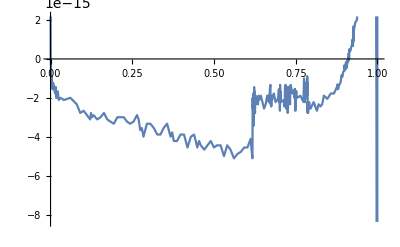

```mathematica
aa=1+I k/2;bb=1/2+I k/2;cc=1;
Plot[Re[(Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]-Gamma[cc]Gamma[cc-aa-bb]/(Gamma[cc-aa]Gamma[cc-bb])Hypergeometric2F1[aa,bb,aa+bb-cc+1,1-r^2]-Gamma[cc]Gamma[aa+bb-cc]/(Gamma[aa]Gamma[bb])(1-r^2)^(cc-aa-bb)Hypergeometric2F1[cc-aa,cc-bb,cc-aa-bb+1,1-r^2]//FullSimplify)/.k->1],{r,0,1}]
```

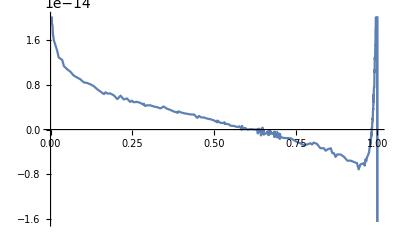

```mathematica
Plot[Im[(Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]-Gamma[cc]Gamma[cc-aa-bb]/(Gamma[cc-aa]Gamma[cc-bb])Hypergeometric2F1[aa,bb,aa+bb-cc+1,1-r^2]-Gamma[cc]Gamma[aa+bb-cc]/(Gamma[aa]Gamma[bb])(1-r^2)^(cc-aa-bb)Hypergeometric2F1[cc-aa,cc-bb,cc-aa-bb+1,1-r^2]//FullSimplify)/.k->1],{r,0,1}]
```

```mathematica
Clear[aa,bb,cc];
repl2F1={Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]->Gamma[cc]Gamma[cc-aa-bb]/(Gamma[cc-aa]Gamma[cc-bb])Hypergeometric2F1[aa,bb,aa+bb-cc+1,1-r^2]+Gamma[cc]Gamma[aa+bb-cc]/(Gamma[aa]Gamma[bb])(1-r^2)^(cc-aa-bb)Hypergeometric2F1[cc-aa,cc-bb,cc-aa-bb+1,1-r^2]/.aa->1+I k/2/.bb->1/2+I k/2/.cc->1, Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),1,r^2]->Gamma[cc]Gamma[cc-aa-bb]/(Gamma[cc-aa]Gamma[cc-bb])Hypergeometric2F1[aa,bb,aa+bb-cc+1,1-r^2]+Gamma[cc]Gamma[aa+bb-cc]/(Gamma[aa]Gamma[bb])(1-r^2)^(cc-aa-bb)Hypergeometric2F1[cc-aa,cc-bb,cc-aa-bb+1,1-r^2]/.aa->1+I k/2/.bb->3/2+I k/2/.cc->1};
```

```mathematica
u0solSSH[t_,r_]=u0sol[t,r]/.repl2F1//FullSimplify
```

1/(k √π)ⅈ 2^(-2-ⅈ k) ⅇ^(ⅈ k t) C[1] (-1/Gamma[-ⅈ k]Gamma[-3/2-ⅈ k] ((-3 ⅈ+2 k) (-ⅈ+k+k r) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),3/2+ⅈ k,1-r^2]+(-ⅈ+k)^2 (-1+r^2) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),5/2+ⅈ k,1-r^2])+1/Gamma[1+ⅈ k]4^(1+ⅈ k) (1-r^2)^(-1/2-ⅈ k) Gamma[1/2+ⅈ k] ((1+2 ⅈ k) Hypergeometric2F1[-(ⅈ k)/2,-1/2 ⅈ (-ⅈ+k),-1/2-ⅈ k,1-r^2]-ⅈ (-ⅈ+k+k r) Hypergeometric2F1[-(ⅈ k)/2,-1/2 ⅈ (ⅈ+k),1/2-ⅈ k,1-r^2]))

```mathematica
u0SSHmode[t_,r_]=(u0solSSH[t,r]/.k->1)-(u0solSSH[t,r]/.k->-1)/.C[1]->cu[1]/2/I//FullSimplify
```

1/(√π)2^(-3-ⅈ) ⅇ^(-ⅈ t) cu[1] (-1/((1+r) Gamma[-ⅈ])(1-8 ⅈ) Gamma[-3/2-ⅈ] ((2+ⅈ) (1+r) (1-r^2)^(-1/2+ⅈ) Hypergeometric2F1[-1/2+ⅈ/2,ⅈ/2,-1/2+ⅈ,1-r^2]+ⅇ^(2 ⅈ t) Hypergeometric2F1[-1/2+ⅈ/2,ⅈ/2,1/2+ⅈ,1-r^2]+(ⅇ^(2 ⅈ t) r-(1-r)^(-1/2+ⅈ) (1+r)^(1/2+ⅈ) ((1+ⅈ)+r)) Hypergeometric2F1[ⅈ/2,1/2+ⅈ/2,1/2+ⅈ,1-r^2])+1/Gamma[ⅈ]2^(2 ⅈ) Gamma[-3/2+ⅈ] ((1+8 ⅈ) ⅇ^(2 ⅈ t) (1-r^2)^(-1/2-ⅈ) ((-2+ⅈ) Hypergeometric2F1[-1/2-ⅈ/2,-ⅈ/2,-1/2-ⅈ,1-r^2]+((1-ⅈ)+r) Hypergeometric2F1[-ⅈ/2,1/2-ⅈ/2,1/2-ⅈ,1-r^2])-(2+3 ⅈ) ((1+ⅈ)+r) Hypergeometric2F1[1/2-ⅈ/2,1-ⅈ/2,3/2-ⅈ,1-r^2]-2 ⅈ (-1+r^2) Hypergeometric2F1[1-ⅈ/2,3/2-ⅈ/2,5/2-ⅈ,1-r^2]))

```mathematica
(* show that SSH limit gives now something finite *)
Collect[Assuming[r<1,Normal[Series[u0SSHmode[t,r],{r,1,1}]]//FullSimplify],{ (1-r)^(1/2+ⅈ),(1-r)^(1/2-ⅈ)}]
```

-(ⅇ^(ⅈ t) (1-r)^(1/2-ⅈ) cu[1] Gamma[-1/2+ⅈ] Gamma[-ⅈ] Sinh[π])/(4 √2 π^(3/2))-(ⅇ^(-ⅈ t) (1-r)^(1/2+ⅈ) cu[1] Gamma[-1/2-ⅈ] Gamma[ⅈ] Sinh[π])/(4 √2 π^(3/2))+(ⅇ^(-ⅈ t) cu[1] ((-1-8 ⅈ) 2^ⅈ Gamma[-3/2+ⅈ] Gamma[-ⅈ]-(1-8 ⅈ) 2^-ⅈ ⅇ^(2 ⅈ t) Gamma[-3/2-ⅈ] Gamma[ⅈ]) Sinh[π])/(8 π^(3/2))

```mathematica
(* verify that limiting result is real by evaluating e.g. at t=0 and r=1 *)
N[(ⅇ^(-ⅈ t) cu[1] ((-1-8 ⅈ) 2^ⅈ Gamma[-3/2+ⅈ] Gamma[-ⅈ]-(1-8 ⅈ) 2^-ⅈ ⅇ^(2 ⅈ t) Gamma[-3/2-ⅈ] Gamma[ⅈ]) Sinh[π])/(8 π^(3/2))/.t->0/.cu[1]->1]//Simplify
```

-0.0223956+0. ⅈ

```mathematica
(* analytic expression for limit of u0 at SSH *)
SSHmode[t_,r_]=Collect[Expand[(Assuming[{r<1,k>0,t>0},Limit[Normal[Series[u0solSSH[t,r]-(u0solSSH[t,r]/.k->-k)/. C[1]->cu[1]/(2I),{r,1,2}]]//FullSimplify,r->1,Direction->"FromBelow"]]//FullSimplify)]/.ⅇ^(ⅈ k t)->Cos[k t]+I Sin[k t]/.ⅇ^(-ⅈ k t)->Cos[k t]- I Sin[k t],{Cos[k t], Sin[k t]}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Sin[k t] (-(ⅈ 2^(-1+ⅈ k) cu[1] Gamma[1/2+ⅈ k] Gamma[-ⅈ k] Sinh[k π])/π^(3/2)+(ⅈ 2^(-1-ⅈ k) cu[1] Gamma[1/2-ⅈ k] Gamma[ⅈ k] Sinh[k π])/π^(3/2))+Cos[k t] ((2^(-1+ⅈ k) cu[1] Gamma[1/2+ⅈ k] Gamma[-ⅈ k] Sinh[k π])/π^(3/2)+(2^(-1-ⅈ k) cu[1] Gamma[1/2-ⅈ k] Gamma[ⅈ k] Sinh[k π])/π^(3/2))

```mathematica
(* simple sanity check for comparison with above *)
N[%/.t->0/.k->1/.cu[1]->1]
```

-0.0223956+0. ⅈ

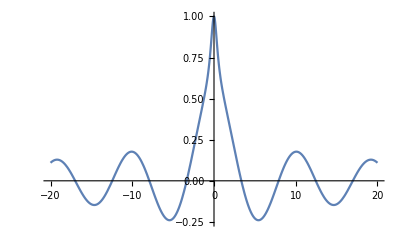

```mathematica
(* here is the sin-coefficent for cu[1]=1 depending on the value of k; looks intriguing since there is definitely a quantization condition that makes the function zero at discrete values of k *)
Plot[Re[(-(ⅈ 2^(-1+ⅈ k)  Gamma[1/2+ⅈ k] Gamma[-ⅈ k] Sinh[k π])/π^(3/2)+(ⅈ 2^(-1-ⅈ k)  Gamma[1/2-ⅈ k] Gamma[ⅈ k] Sinh[k π])/π^(3/2))],{k,-20,20},PlotRange->{-0.25,1}]
```

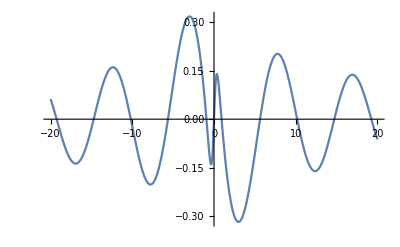

```mathematica
(* same plot for the cos-coefficient *)
Plot[Re[ ((2^(-1+ⅈ k)  Gamma[1/2+ⅈ k] Gamma[-ⅈ k] Sinh[k π])/π^(3/2)+(2^(-1-ⅈ k)  Gamma[1/2-ⅈ k] Gamma[ⅈ k] Sinh[k π])/π^(3/2))],{k,-20,20}]
```

```mathematica
USSH16[t_]=Sum[SSHmode[t,r]/.cu[1]->cu[n],{n,1,16}];
```

#### Plot real and imaginary parts of u0 near the SSH and show that imaginary part vanishes

```mathematica
(* this is the plot of the WRONG expansion near SSH *) 
Plot3D[Re[u0modessh[t,r]/.k->1/.cu[1]->1],{t,0,2Pi},{r,0.9,1}]
```

-Graphics3D-

```mathematica
(* still, the imaginary part is graphically zero to at least 15 orders of magnitude *)
Plot3D[Im[u0modessh[t,r]/.k->1/.cu[1]->1],{t,0,2Pi},{r,0.9,1},PlotRange->{-10^(-15),10^(-15)}]
```

-Graphics3D-

#### Compare exact plots with origin and SSH expansions

```mathematica
(* near origin expansion *)
Plot3D[u0modeorigin[t,r]/.k->1/.cu[1]->1,{t,0,2Pi},{r,0,1}]
```

-Graphics3D-

```mathematica
(* exact solution *)
Plot3D[Re[(u0sol[t,r]/.k->1)-(u0sol[t,r]/.k->-1)/. C[1] ->1/2/I],{t,0,2Pi},{r,0,1}]
```

-Graphics3D-

```mathematica
(* difference between exact solution and origin expansion shows that up to r=1/2 better than 1% accuracy is ok *)
Plot3D[Re[(u0sol[t,r]/.k->1)-(u0sol[t,r]/.k->-1)/. C[1] ->1/2/I]-u0modeorigin[t,r]/.k->1/.cu[1]->1,{t,0,2Pi},{r,0,1},PlotRange->{-0.01,0.01}]
```

-Graphics3D-

```mathematica
(* difference between exact solution and SSH expansion shows that the latter misses a fundamental Fourier mode but not much else *)
Plot3D[Re[(u0sol[t,r]/.k->1)-(u0sol[t,r]/.k->-1)/. C[1] ->1/2/I],{t,0,2Pi},{r,0.9,1}]
```

-Graphics3D-

```mathematica
(* the boundary value derives above correctly captures this behavior *)
Plot3D[Re[SSHmode[t,r]/.k->1/.cu[1]->1],{t,0,2Pi},{r,0.9,1}]
```

-Graphics3D-

```mathematica
(* the difference between the boundary mode and the exact solution indeed vanishes at the SSH but then quickly is non-zero in the interior *)
Plot3D[Re[SSHmode[t,r]/.k->1/.cu[1]->1]-Re[(u0sol[t,r]/.k->1)-(u0sol[t,r]/.k->-1)/. C[1] ->1/2/I],{t,0,2Pi},{r,0.99,1},PlotRange->{-0.01,0.01}]
```

-Graphics3D-

```mathematica
(* adding the boundary mode to the WRONG SSH expansion gives actually a somewhat decent approximation for the function u0 close to the SSH *) 
Plot3D[Re[SSHmode[t,r]/.k->1/.cu[1]->1]+Re[u0modessh[t,r]/.k->1/.cu[1]->1 ]-Re[(u0sol[t,r]/.k->1)-(u0sol[t,r]/.k->-1)/. C[1] ->1/2/I],{t,0,2Pi},{r,0.99,1},PlotRange->{-0.01,0.01}]
```

-Graphics3D-

```mathematica
(* show that hypergeometric trafo used above indeed works as an identity in the whole plane but with numerical inaccuracies near the SSH *)
Plot3D[Re[(u0sol[t,r]/.k->1)-(u0sol[t,r]/.k->-1)/. C[1] ->1/2/I]-Re[u0SSHmode[t,r]/.cu[1]->1],{t,0,2Pi},{r,0,1},PlotRange->{-10^(-10),10^(-10)}]
```

-Graphics3D-

```mathematica
u0sol[t,r]
```

1/k ⅇ^(ⅈ k t) C[1] ((-ⅈ+k+k r) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),1,r^2]+(-ⅈ+k) (-1+r^2) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),1,r^2])

#### Here is the full solution for u0[t,r] with all Fourier modes, Taylor expanded around the origin to 10 orders

```mathematica
u0origin[t_,r_]=Normal[Sum[Series[(u0sol[r]/.k->n k)-(u0sol[r]/.k->-n k)//Simplify,{r,0,10}]/.C[1]->cu[n]/2/I//FullSimplify,{n,1,Infinity}]]
```

0

```mathematica
(* explicit example with 16 Fourier modes *)
u016[t_,r_]=Normal[Sum[Series[(u0sol[r]/.k->n k)-(u0sol[r]/.k->-n k),{r,0,10}]/.C[1]->cu[n]/2/I,{n,1,16}]];
```

### Do the same for v0

```mathematica
v0modeorigin[t_,r_]=Normal[Series[(v0sol[r])-(v0sol[r]/.k->-k)//FullSimplify,{r,0,10}]/.C[1]->cu[1]/2/I//FullSimplify]
```

0

#### Note that v0 near the SSH diverges; the imaginary part is zero, as it should be

```mathematica
v0modessh[t_,r_]=Normal[Assuming[r<1,Series[(v0sol[r])-(v0sol[r]/.k->-k)//Simplify,{r,1,0}]/.C[1]->cu[1]/2/I]]//Simplify//FullSimplify
```

0

```mathematica
Plot3D[Re[v0modessh[t,r]/.k->1/.cu[1]->1],{t,0,2Pi},{r,0.9,1}]
```

-Graphics3D-

```mathematica
Plot3D[Im[v0modessh[t,r]/.k->1/.cu[1]->1],{t,0,2Pi},{r,0.9,1},PlotRange->{-10^(-10),10^(-10)}]
```

-Graphics3D-

#### Hypergymnastics

```mathematica
(* we can manipulate v0 using th2 2F1 identity from above... *)
v0solSSH[t_,r_]=v0sol[t,r]/.repl2F1//FullSimplify
```

1/(k √π)2^(-2-ⅈ k) ⅇ^(ⅈ k t) C[1] (1/Gamma[-ⅈ k]ⅈ Gamma[-3/2-ⅈ k] ((3 ⅈ-2 k) (ⅈ+k (-1+r)) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (1+ⅈ k),3/2+ⅈ k,1-r^2]+(-ⅈ+k)^2 (-1+r^2) Hypergeometric2F1[1+(ⅈ k)/2,1/2 (3+ⅈ k),5/2+ⅈ k,1-r^2])-1/Gamma[1+ⅈ k]4^(1+ⅈ k) (1-r^2)^(-1/2-ⅈ k) Gamma[1/2+ⅈ k] ((ⅈ-2 k) Hypergeometric2F1[-(ⅈ k)/2,-1/2 ⅈ (-ⅈ+k),-1/2-ⅈ k,1-r^2]+(-ⅈ+k-k r) Hypergeometric2F1[-(ⅈ k)/2,-1/2 ⅈ (ⅈ+k),1/2-ⅈ k,1-r^2]))

```mathematica
(* ... but the near SSH expansion still yields a term that blows up like 1/Sqrt[1-r] *)
Assuming[{r<1t>0,k>0},Normal[Series[v0solSSH[t,r],{r,1,1}]]//FullSimplify]
```

(ⅇ^(ⅈ k t) C[1] ((2^(-ⅈ k) Gamma[-1/2-ⅈ k])/Gamma[1-ⅈ k]+(2 √2 (1-r)^(-1/2-ⅈ k) Gamma[1/2+ⅈ k])/Gamma[1+ⅈ k]))/(2 √π)

#### Here is the full solution for v0[t,r] with all Fourier modes, Taylor expanded around the origin to 10 orders

```mathematica
v0origin[t_,r_]=Normal[Sum[Series[(v0sol[r]/.k->n k)-(v0sol[r]/.k->-n k)//Simplify,{r,0,10}]/.C[1]->cu[n]/2/I//FullSimplify,{n,1,Infinity}]]
```

0

```mathematica
Collect[Expand[Assuming[{r<1,k>0,t>0},Normal[Series[v0solSSH[t,r]-(v0solSSH[t,r]/.k->-k)/. C[1]->cu[1]/(2I),{r,1,1}]]//Simplify]/.+(2^(-ⅈ k) (-(ⅇ^(2 ⅈ k t) (-3 ⅈ+2 k) Gamma[-3/2-ⅈ k])/Gamma[-ⅈ k]+(2^(2 ⅈ k) (3 ⅈ+2 k) Gamma[-3/2+ⅈ k])/Gamma[ⅈ k]))/k->0/.cu[1]->1]/.ⅇ^(ⅈ k t)->Cos[k t]+I Sin[k t]/.ⅇ^(-ⅈ k t)->Cos[k t]- I Sin[k t],{Sin[k t], Cos[k t]}]
```

Cos[k t] ((ⅈ (1-r)^(-1/2+ⅈ k) Gamma[1/2-ⅈ k])/(√(2 π) Gamma[1-ⅈ k])-(ⅈ (1-r)^(-1/2-ⅈ k) Gamma[1/2+ⅈ k])/(√(2 π) Gamma[1+ⅈ k]))+(((1-r)^(-1/2+ⅈ k) Gamma[1/2-ⅈ k])/(√(2 π) Gamma[1-ⅈ k])+((1-r)^(-1/2-ⅈ k) Gamma[1/2+ⅈ k])/(√(2 π) Gamma[1+ⅈ k])) Sin[k t]

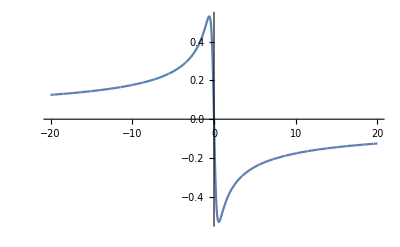

```mathematica
(* dropping the r-dependent piece of the cos-term I get a function that does not vanish anywhere except at k=0 *)
Plot[Re[((ⅈ  Gamma[1/2-ⅈ k])/(√(2 π) Gamma[1-ⅈ k])-(ⅈ  Gamma[1/2+ⅈ k])/(√(2 π) Gamma[1+ⅈ k]))],{k,-20,20}]
```

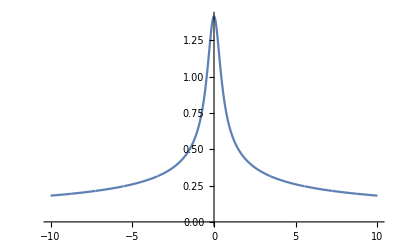

```mathematica
(* same for the sin-term *)
Plot[Re[(Gamma[1/2-ⅈ k]/(√(2 π) Gamma[1-ⅈ k])+Gamma[1/2+ⅈ k]/(√(2 π) Gamma[1+ⅈ k]))],{k,-10,10},PlotRange->{0,Sqrt[2]}]
```

```mathematica
v016[t_,r_]=Normal[Sum[Series[(v0sol[t,r]/.k->n k)-(v0sol[t,r]/.k->-n k),{r,0,10}]/.C[1]->cu[n]/2/I,{n,1,16}]];
```

## Show that solutions fail to be regular at r=1 (if k is real), though u0 is regular

```mathematica
Assuming[r<1,Series[pisol[r],{r,1,1}]//FullSimplify]
```

O[r-1]^0+(-1+r)^(-ⅈ k) ((ⅇ^(-k (π-ⅈ t)) √(π/2) C[1] Sech[k π])/(k Gamma[1/2-ⅈ k] Gamma[ⅈ k] √(r-1))+√O[r-1])

```mathematica
Assuming[r<1,Series[psisol[r],{r,1,1}]//FullSimplify]
```

((ⅈ 2^(-1-ⅈ k) ⅇ^(ⅈ k t) √π C[1] Sech[k π])/(k Gamma[-1-ⅈ k] Gamma[3/2+ⅈ k])-(ⅈ 2^(-2-ⅈ k) ⅇ^(ⅈ k t) √π C[1] Sech[k π] (r-1))/(k Gamma[-3-ⅈ k] Gamma[5/2+ⅈ k])+O[r-1]^(3/2))+(-1+r)^(-ⅈ k) ((ⅇ^(-k (π-ⅈ t)) √(π/2) C[1] Sech[k π])/(k Gamma[1/2-ⅈ k] Gamma[ⅈ k] √(r-1))-(ⅇ^(-k (π-ⅈ t)) √(2 π) C[1] Sech[k π] √(r-1))/(k Gamma[1/2-ⅈ k] Gamma[ⅈ k])+O[r-1]^(3/2))

### Also v0 is singular at r=1

```mathematica
Assuming[r<1,Series[v0sol[t,r],{r,1,0}]//FullSimplify]
```

(1+(-1+r)^(-ⅈ k)) 1/(√O[r-1])

### However, u0 is regular at r=1

```mathematica
Assuming[r<1,Series[u0sol[t,r],{r,1,1}]//FullSimplify]
```

(2^(-1-ⅈ k) ⅇ^(ⅈ k t) √π (1+k (2 ⅈ+k (-1+r))) C[1] Sech[k π])/(Gamma[1-ⅈ k] Gamma[3/2+ⅈ k])+(-1+r)^(-ⅈ k) √O[r-1]

## Get Psi at origin as prediction for boundary data

```mathematica
psi0origin[t_,r_]=Normal[Series[(v0origin[t,r]-u0origin[t,r])/(2r^2),{r,0,10}]];
```

```mathematica
psi016[t_,r_]=Normal[Series[(v016[t,r]-u016[t,r])/(2r^2),{r,0,10}]];
```

```mathematica
psiatorigin=Normal[Series[psi016[t,r],{r,0,0}]//Simplify]//FullSimplify
```

1/(4 r)(k r Cos[k t] cu[1]+2 k r Cos[2 k t] cu[2]+3 k r Cos[3 k t] cu[3]+4 k r Cos[4 k t] cu[4]+5 k r Cos[5 k t] cu[5]+6 k r Cos[6 k t] cu[6]+7 k r Cos[7 k t] cu[7]+8 k r Cos[8 k t] cu[8]+9 k r Cos[9 k t] cu[9]+10 k r Cos[10 k t] cu[10]+11 k r Cos[11 k t] cu[11]+12 k r Cos[12 k t] cu[12]+13 k r Cos[13 k t] cu[13]+14 k r Cos[14 k t] cu[14]+15 k r Cos[15 k t] cu[15]+16 k r Cos[16 k t] cu[16]+(2+r) cu[1] Sin[k t]+(2+r) cu[2] Sin[2 k t]+(2+r) cu[3] Sin[3 k t]+(2+r) cu[4] Sin[4 k t]+(2+r) cu[5] Sin[5 k t]+(2+r) cu[6] Sin[6 k t]+(2+r) cu[7] Sin[7 k t]+(2+r) cu[8] Sin[8 k t]+(2+r) cu[9] Sin[9 k t]+(2+r) cu[10] Sin[10 k t]+(2+r) cu[11] Sin[11 k t]+(2+r) cu[12] Sin[12 k t]+(2+r) cu[13] Sin[13 k t]+(2+r) cu[14] Sin[14 k t]+(2+r) cu[15] Sin[15 k t]+(2+r) cu[16] Sin[16 k t])